-Graphics-

```mathematica
cannon[L1_,L2_]:=Sort[{L1,L2}][[1]]
```

```mathematica
multipic[L_]:=Style[Show[Map[picc,L]],Antialiasing->False]
```

```mathematica
picc[L_]:=Graphics[{LightOrange,Map[Rectangle[#-{1,1},#]&,L~Join~{{1,1},{1,5},{5,5},{5,1}}],Black,
Table[Line[{{0,i},{width,i}}],{i,0,height}],Table[Line[{{i,0},{i,height}}],{i,0,width}],Red,AbsoluteThickness[2],Line[Map[#-{1/2,1/2}&,L]]
},ImageSize->20{width,height}]
```

```mathematica
pic[L_]:=Style[Graphics[{
Table[Line[{{0,i},{width,i}}],{i,0,height}],Table[Line[{{i,0},{i,height}}],{i,0,width}],Red,AbsoluteThickness[2],Line[Map[#-{1/2,1/2}&,L]]
},ImageSize->20{width,height}],Antialiasing->False]
```

```mathematica
probpic[L_]:=Style[Graphics[{LightGreen, Map[Rectangle[#-{1,1},#]&,L],Black,
Table[Line[{{0,i},{width,i}}],{i,0,height}],Table[Line[{{i,0},{i,height}}],{i,0,width}]
},ImageSize->20{width,height}],Antialiasing->False]
```

```mathematica
bbi[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=(Max[Min[x1,x2],Min[x3,x4]]<Min[Max[x1,x2],Max[x3,x4]])&&(Max[Min[y1,y2],Min[y3,y4]]<Min[Max[y1,y2],Max[y3,y4]])
```

```mathematica
det[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=Det[{{x1,y1,1},{x2,y2,1},{x3,y3,1}}]
```

```mathematica
inter[{{x1_,y1_},{x2_,y2_}},{{x3_,y3_},{x4_,y4_}}]:=(det[{x1,y1},{x2,y2},{x3,y3}]det[{x1,y1},{x2,y2},{x4,y4}]<0)&&(det[{x3,y3},{x4,y4},{x1,y1}]det[{x3,y3},{x4,y4},{x2,y2}]<0)&&bbi[{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
```

```mathematica
intersect[L_]:=Apply[Or,Map[inter[#[[1]],#[[2]]]&,Flatten[Outer[List,Partition[L,2,1],Partition[L,2,1],1],1]]]
```

```mathematica
convert[L_]:=Table[Position[L,{ii,jj}][[1,1]],{ii,1,width},{jj,1,height}]
```

```mathematica
somepic[L_]:=Style[Graphics[{
Table[Line[{{0,i},{width,i}}],{i,0,height}],Table[Line[{{i,0},{i,height}}],{i,0,width}],Map[Text[pieces[#[[3]]],{#[[1]]-1/2,#[[2]]-1/2}]&,L]
},ImageSize->33*width],Antialiasing->False]
```

```mathematica
fullpic[L_]:=Style[Graphics[{
Table[Line[{{0,i},{width,i}}],{i,0,height}],Table[Line[{{i,0},{i,height}}],{i,0,width}],MapIndexed[Text[#1,#2-{1/2,1/2}]&,Map[pieces,convert[L],{2}],{2}]
},ImageSize->33*width],Antialiasing->False]
```

```mathematica
perms[L_]:=(temp=Complement[Flatten[Table[{i,j},{i,1,width},{j,1,height}],1],{{1,1},{1,5},{5,5},{5,1}},Union[Flatten[L,1]]];Map[{First[temp]}~Join~#~Join~{First[temp]}&,Permutations[Rest[temp]]])
```

```mathematica
queenmoves={{1,0},{2,0},{3,0},{4,0},{-1,0},{-2,0},{-3,0},{-4,0},{0,1},{0,2},{0,3},{0,4},{0,-1},{0,-2},{0,-3},{0,-4},{1,1},{2,2},{3,3},{1,-1},{2,-2},{3,-3},{-1,1},{-2,2},{-3,3},{-1,-1},{-2,-2},{-3,-3}};
```

```mathematica
allqueen[L_]:=Apply[And,Map[MemberQ[queenmoves,#]&,L]]
```

```mathematica
queenposs[L_]:=Select[perms[L],neverreverse[#]&&allqueen[Rest[#-RotateRight[#]]]&&{#[[2]],#[[-2]]}==Sort[{#[[2]],#[[-2]]}]&]
```

```mathematica
pieces[1]=Style["b",FontSize->30,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Red];
pieces[2]=Style["n",FontSize->30,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Green];
pieces[3]=Style["k",FontSize->30,FontFamily->"Chess Cases",FontSlant->Plain];
pieces[4]=Style["r",FontSize->30,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Blue];
pieces[5]=Style["q",FontSize->30,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->RGBColor[1,3/4,0]];
```

```mathematica
neverreverse[L_]:=Not[MemberQ[Map[#/Sqrt[#.#]&,Drop[L-RotateLeft[L],-1]]+RotateRight[Map[#/Sqrt[#.#]&,Drop[L-RotateLeft[L],-1]]],{0,0}]]
```

```mathematica
notreverse[L_]:=Not[MemberQ[Rest[Map[#/Sqrt[#.#]&,Drop[L-RotateLeft[L],-1]]+RotateRight[Map[#/Sqrt[#.#]&,Drop[L-RotateLeft[L],-1]]]],{0,0}]]
```

```mathematica
f:=Module[{},
 width=5;
height=5;
solns={};stack=Map[{#}&,Complement[Flatten[Table[{i,j},{i,1,width},{j,1,height}],1],{{1,1},{1,5},{5,1},{5,5}}]];
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
If[Length[cur]-1≤6,
If[First[cur]==Last[cur]&&Length[cur]>3,If[cannon[cur[[2]],cur[[-2]]]==cur[[2]],AppendTo[solns,cur]],If[First[cur]=!=Last[cur]||(First[cur]==Last[cur]&&Length[cur])<2,
poss=Map[Last[cur]+#&,moves];
poss=Select[poss,1≤#[[1]]≤width&&1≤#[[2]]≤height&&Not[MemberQ[{{1,1},{1,5},{5,1},{5,5}},#]]&];
poss=Complement[poss,Rest[cur]];
poss=Select[poss,cannon[First[cur],#]==First[cur]&];
poss=Select[poss,notreverse[cur~Join~{#}]&];
(*poss=Select[poss,Not[intersect[cur~Join~{#}]]&];*)
stack=stack~Join~Map[cur~Join~{#}&,poss];
]]]]]
```

```mathematica
moves={{1,2},{2,1},{1,-2},{2,-1},{-1,2},{-2,1},{-1,-2},{-2,-1}};
```

```mathematica
f
```

```mathematica
knight=solns;
```

```mathematica
Length[knight]
```

142

```mathematica
moves={{1,1},{2,2},{3,3},{1,-1},{2,-2},{3,-3},{-1,1},{-2,2},{-3,3},{-1,-1},{-2,-2},{-3,-3}};
```

```mathematica
f
```

```mathematica
bishop=solns;
```

```mathematica
bishop=Select[bishop,neverreverse];
```

```mathematica
Length[bishop]
```

128

```mathematica
combined=Flatten[Outer[List,bishop,knight,1],1];
```

```mathematica
combined=Select[combined,Intersection[#[[1]],#[[2]]]=={}&];
```

```mathematica
combined=Select[combined,Length[Flatten[#,1]]-2≤11&];
```

```mathematica
Length[combined]
```

1130

```mathematica
moves={{1,1},{1,-1},{-1,1},{-1,-1},{1,0},{-1,0},{0,1},{0,-1}};
```

```mathematica
f
```

```mathematica
king=solns;
```

```mathematica
Length[king]
```

1315

```mathematica
combined=Flatten[Outer[Append,combined,king,1],1];
```

```mathematica
combined=Select[combined,Intersection[#[[1]],#[[2]]]=={}&&Intersection[#[[1]],#[[3]]]=={}&&Intersection[#[[2]],#[[3]]]=={}&];
```

```mathematica
combined=Select[combined,Length[Flatten[#,1]]-3≤14&];
```

```mathematica
Length[combined]
```

12224

```mathematica
moves={{1,0},{2,0},{3,0},{4,0},{-1,0},{-2,0},{-3,0},{-4,0},{0,1},{0,2},{0,3},{0,4},{0,-1},{0,-2},{0,-3},{0,-4}};
```

```mathematica
f
```

```mathematica
rook=solns;
```

```mathematica
rook=Select[rook,neverreverse];
```

```mathematica
Length[rook]
```

655

```mathematica
combined2={};
For[ii=1,ii≤Length[combined],ii++,
For[jj=1,jj≤Length[rook],jj++,
t1=combined[[ii]];
t2=rook[[jj]];
If[Intersection[t1[[1]],t2]=={}&&Intersection[t1[[2]],t2]=={}&&Intersection[t1[[3]],t2]=={},
AppendTo[combined2,Append[combined[[ii]],rook[[jj]]]]]]];
```

```mathematica
combined2=Select[combined2,Length[Flatten[#,1]]-4≤18&];
```

```mathematica
Length[combined2]
```

9860

```mathematica
AA={};
For[ii=1,ii≤Length[combined2],ii++,
Q=queenposs[combined2[[ii]]];
For[jj=1,jj≤Length[Q],jj++,
AppendTo[AA,Append[combined2[[ii]],Q[[jj]]]]]];
```

```mathematica
Length[AA]
```

2512

```mathematica
For[i=1,i≤Length[AA],i++,
AA=ReplacePart[AA,{i,5}->AA[[i,5]]~Join~{{1,1},{1,5},{5,1},{5,5}}]]
```

```mathematica
AA[[1]]
```

{{{1,2},{2,1},{3,2},{2,3},{1,2}},{{1,4},{2,2},{4,1},{3,3},{1,4}},{{2,4},{2,5},{3,4},{2,4}},{{4,2},{4,4},{5,4},{5,2},{4,2}},{{1,3},{3,1},{5,3},{3,5},{4,5},{4,3},{1,3},{1,1},{1,5},{5,1},{5,5}}}

```mathematica
For[k1=1,k1≤3,k1++,
For[k2=k1+1,k2≤4,k2++,
For[k3=k2+1,k3≤5,k3++,
Print[k1,k2,k3];
For[i1=1,i1≤3,i1++,
For[j1=i1,j1≤3,j1++,
If[Not[MemberQ[{{1,1},{1,5},{5,1},{5,5}},{i1,j1}]],
For[i2=1,i2≤width,i2++,
For[j2=1,j2≤height,j2++,
If[Not[MemberQ[{{1,1},{1,5},{5,1},{5,5}},{i2,j2}]],
For[i3=1,i3≤width,i3++,
For[j3=1,j3≤height,j3++,
If[Not[MemberQ[{{1,1},{1,5},{5,1},{5,5}},{i3,j3}]],
B=Select[AA,MemberQ[#[[k1]],{i1,j1}]&&MemberQ[#[[k2]],{i2,j2}]&&MemberQ[#[[k3]],{i3,j3}]&];
If[Length[B]==1,Print[];Print[somepic[{{i1,j1,k1},{i2,j2,k2},{i3,j3,k3}}]];Print[fullpic[B[[1]]]]]]]]]]]]]]]]]
```

## BNK

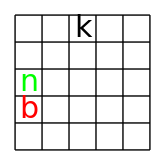

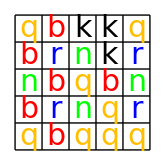

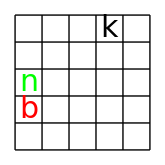

-Graphics-

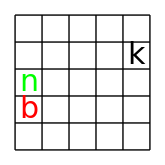

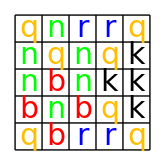

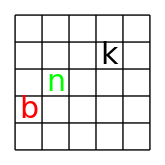

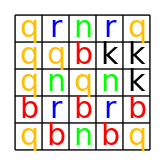

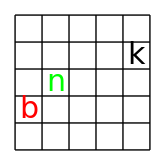

-Graphics-

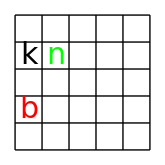

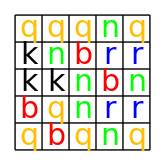

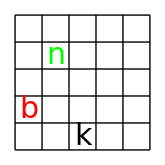

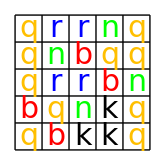

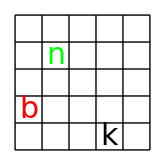

-Graphics-

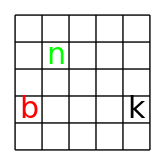

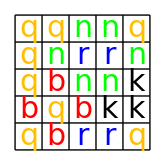

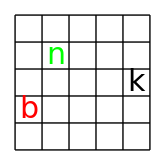

-Graphics-

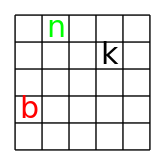

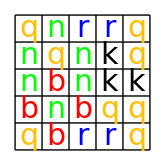

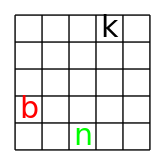

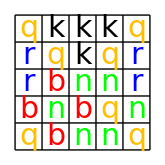

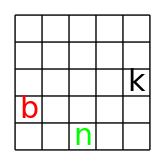

-Graphics-

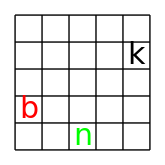

-Graphics-

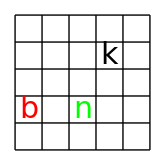

-Graphics-

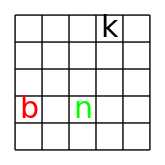

-Graphics-

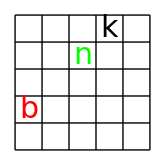

-Graphics-

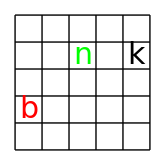

-Graphics-

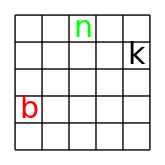

-Graphics-

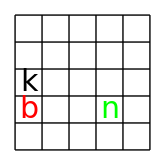

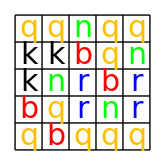

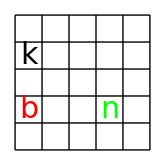

-Graphics-

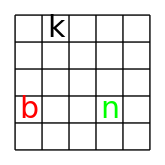

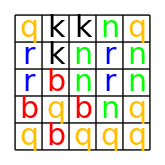

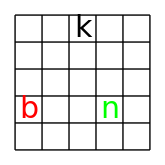

-Graphics-

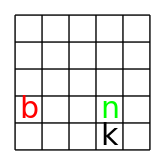

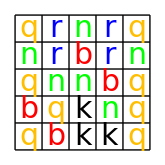

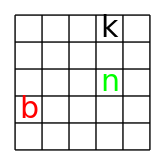

-Graphics-

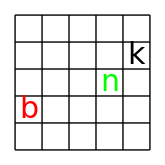

-Graphics-

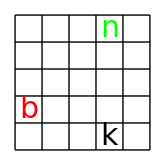

-Graphics-

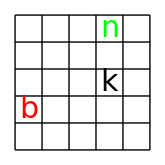

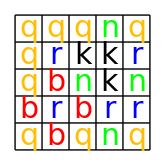

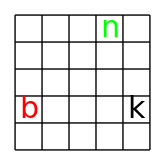

-Graphics-

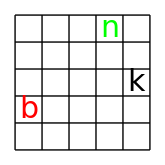

-Graphics-

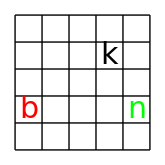

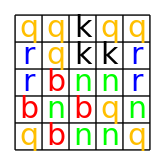

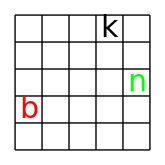

-Graphics-

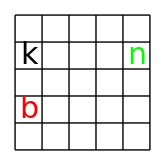

-Graphics-

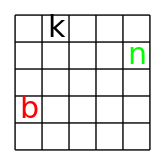

-Graphics-

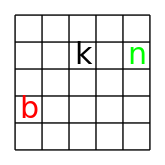

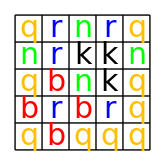

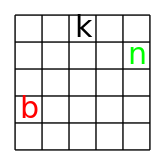

-Graphics-

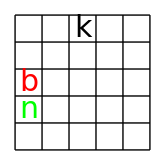

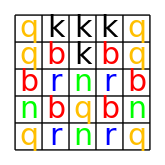

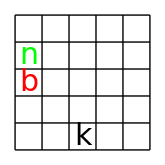

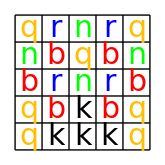

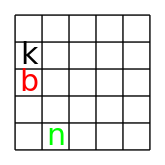

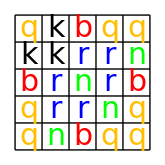

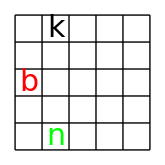

-Graphics-

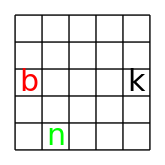

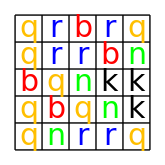

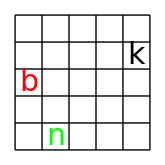

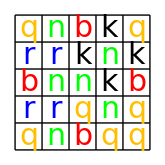

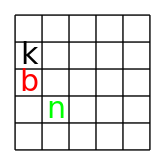

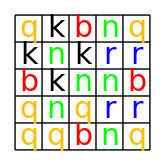

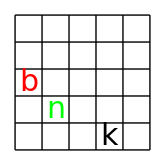

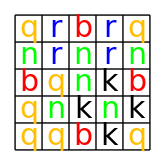

-Graphics-

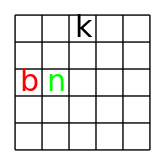

-Graphics-

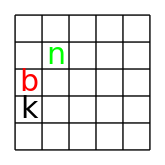

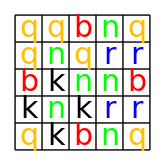

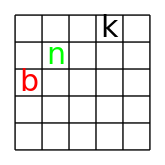

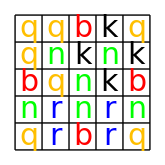

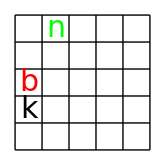

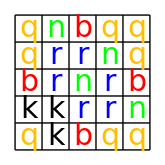

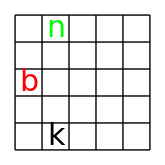

-Graphics-

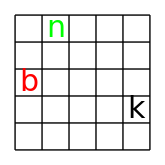

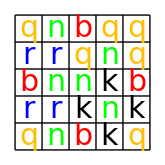

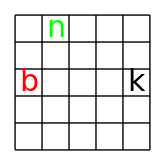

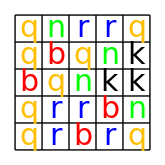

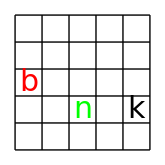

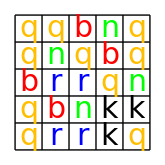

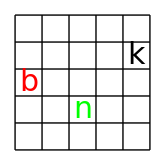

-Graphics-

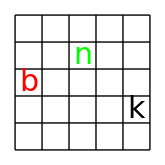

-Graphics-

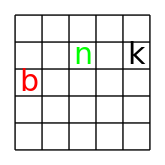

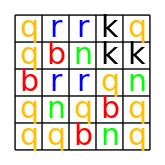

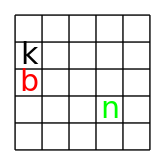

-Graphics-

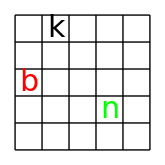

-Graphics-

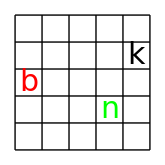

-Graphics-

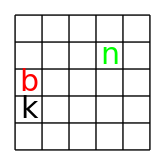

-Graphics-

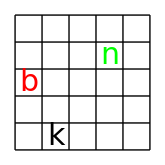

-Graphics-

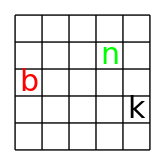

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«233 more identical outputs»

## BNR

-Graphics-

-Graphics-

-Graphics-

«137 more identical outputs»

## BNQ

-Graphics-

-Graphics-

-Graphics-

«157 more identical outputs»

## BKR

-Graphics-

-Graphics-

-Graphics-

«201 more identical outputs»

## BKQ

-Graphics-

-Graphics-

-Graphics-

«101 more identical outputs»

## BRQ

-Graphics-

-Graphics-

-Graphics-

«149 more identical outputs»

## NKR

-Graphics-

-Graphics-

-Graphics-

«211 more identical outputs»

## NKQ

-Graphics-

-Graphics-

-Graphics-

«235 more identical outputs»

## NRQ

-Graphics-

-Graphics-

-Graphics-

«167 more identical outputs»

## KRQ

-Graphics-

-Graphics-

-Graphics-

«201 more identical outputs»

## 4x5

```mathematica
Map[multipic,A]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

-Graphics-

-Graphics-

«227 more identical outputs»

## 3x7

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## 5x5

-Graphics-

-Graphics-